```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"..","Data"}]];

LAmodelParametersImport=Import["LWI_output.csv"]; 
(*Convert the data into an Association for easier access*)
columnNames=LAmodelParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=LAmodelParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
LAmodelParameters=AssociationThread[columnNames->#]&/@dataRows;

FLmodelParametersImport=Import["Jacksonville_output.csv"]; 
(*Convert the data into an Association for easier access*)
columnNames=FLmodelParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=FLmodelParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
FLmodelParameters=AssociationThread[columnNames->#]&/@dataRows;

LAhydroParametersImport=Import["USGS_gage_hydro_variables_lwi-transition-zone.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=LAhydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=LAhydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
LAhydroParameters=AssociationThread[columnNames->#]&/@dataRows;

FLhydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=FLhydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=FLhydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
FLhydroParameters=AssociationThread[columnNames->#]&/@dataRows;
```

```mathematica
(*Data NSE *)
```

```mathematica
NSEdata =Join[Drop[LAmodelParametersImport[[All,8]],1],
Drop[FLmodelParametersImport[[All,8]],1]];
Median[NSEdata ]
Mean[NSEdata ]
Sort[Drop[LAmodelParametersImport[[All,8]],1]];
Sort[Drop[FLmodelParametersImport[[All,8]],1]];
```

0.975886

0.960407

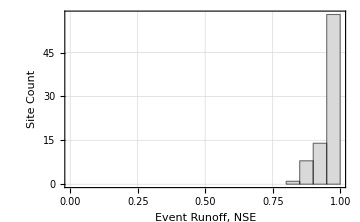

```mathematica
NSE = Histogram[NSEdata,{0,1,0.05},(*Bin width of 0.05 with x-axis from 0 to 1*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, NSE","Site Count"},PlotRange->{{0,1},Automatic},(*Ensures x-axis stays between 0 and 1*)ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},(*Gray bars with black outlines*)ImageSize->Medium,PlotTheme->"Detailed"]
```

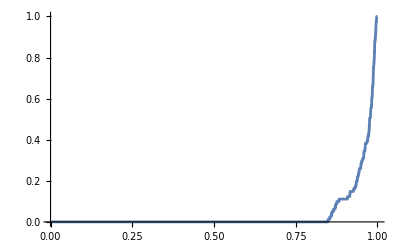

```mathematica
Plot[CDF[EmpiricalDistribution[NSEdata],x],{x,0,1},Exclusions->None,PlotRange->All]
```

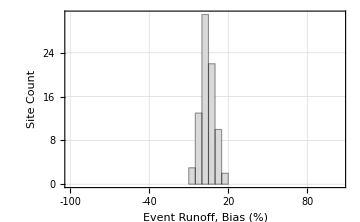

4.59788

4.78091

```mathematica
PBIASdata =Join[Drop[LAmodelParametersImport[[All,10]],1],
Drop[FLmodelParametersImport[[All,10]],1]];
PBIAS=Histogram[PBIASdata ,{Range[-100,105,5]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, Bias (%)","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[-100,100,20],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
PBIASdata //Median
PBIASdata //Mean
```

0.057655

0.83217

0.83217

0.184136

0.13526

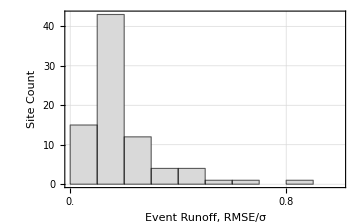

{0.057655,0.0586195,0.0666533,0.0708648,0.0723467,0.0727953,0.0802662,0.0816763,0.0828789,0.0843487,0.0883656,0.0910821,0.0932513,0.09333,0.0995123,0.101914,0.101951,0.10352,0.103895,0.105327,0.105868,0.107036,0.109823,0.110202,0.112105,0.11319,0.117047,0.119129,0.120418,0.122942,0.124109,0.124845,0.125841,0.127142,0.127582,0.128098,0.128588,0.131139,0.13281,0.134995,0.13526,0.137237,0.137899,0.138088,0.138921,0.141059,0.150762,0.153197,0.153663,0.15411,0.162193,0.171817,0.18094,0.183009,0.191267,0.194437,0.197386,0.197915,0.20125,0.201739,0.206574,0.210255,0.212696,0.216267,0.223488,0.230618,0.235672,0.24444,0.263431,0.284249,0.316167,0.328435,0.341479,0.356571,0.426143,0.453907,0.463811,0.490298,0.513613,0.609429,0.83217}

```mathematica
RMSEdata =Join[Drop[LAmodelParametersImport[[All,7]],1],
Drop[FLmodelParametersImport[[All,7]],1]];
Sigmadata2 =Join[Drop[LAhydroParametersImport[[All,22]],1],
Drop[FLhydroParametersImport[[All,22]],1]];
Min[ RMSEdata /√Sigmadata2]
Max[ RMSEdata /√Sigmadata2]
Max[ RMSEdata /√Sigmadata2]
Mean[ RMSEdata /√Sigmadata2]
Median[ RMSEdata /√Sigmadata2]
NRMSE=Histogram[ RMSEdata /√Sigmadata2,{Range[0,1,.1]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Event Runoff, RMSE/σ ","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[0,3.2,.2],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
Sort[RMSEdata /√Sigmadata2]
```

```mathematica
(*https://journals.ametsoc.org/view/journals/hydr/19/11/jhm-d-18-0139_1.xml#:~:text=VIC%20model%20consists%20of%20two%20modes:%20a,for%20both%20water%20and%20energy%20balance%20simulations.*)
```

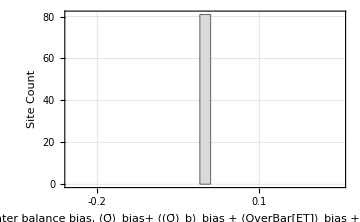

```mathematica
zerosList=ConstantArray[0,81];
RBias=Histogram[zerosList,{Range[-.25,.25,.02]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"Water balance bias, ⟨Q̄⟩_bias+ ⟨(Q̄)_b⟩_bias + ⟨OverBar[ET]⟩_bias +σ_(Q̄)^2l_bias","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],(*Gray bars,black outline*)FrameTicks->{{Automatic,None},(*x-axis ticks every 20 units*){Range[-.5,.5,.1],None}  (*y-axis with automatic ticks*)},LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

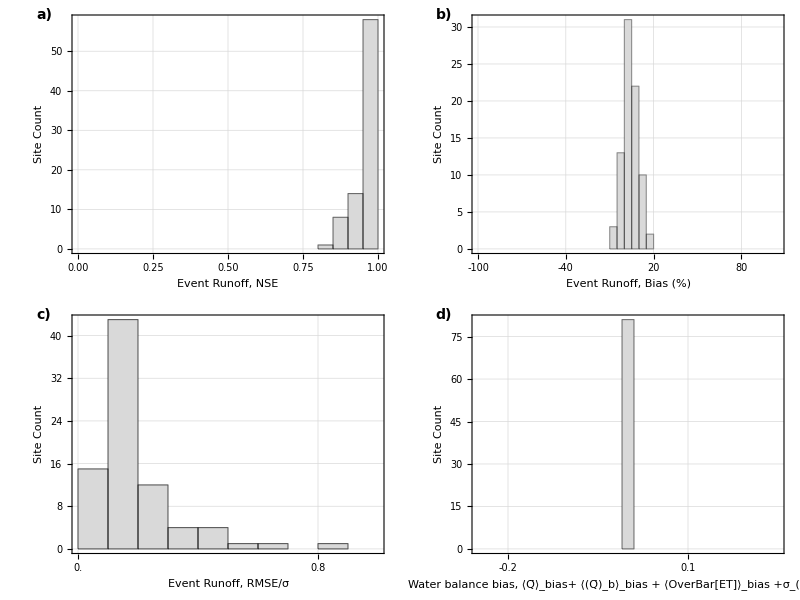

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]

(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[NSE,"a)"],labeledPlot[PBIAS,"b)"]},{labeledPlot[NRMSE,"c)"],labeledPlot[RBias,"d)"]}},Spacings->2]
```

```mathematica
(*Export the grid as EPS*)Export["Figure8.pdf",grid]
```

Figure8.pdf

## Parameter Value

```mathematica
wdata =Join[Drop[LAmodelParametersImport[[All,4]],1],
Drop[FLmodelParametersImport[[All,4]],1]]*10
```

{777.711,455.614,115.352,842.461,404.458,497.724,1097.28,204.1,685.871,309.442,472.811,168.014,133.47,216.185,172.211,171.42,353.256,419.207,316.015,1863.25,2899.78,338.718,186.04,510.513,312.29,2251.07,3115.07,2856.39,517.72,477.757,1609.23,1918.81,702.624,475.828,912.254,353.668,961.952,289.031,291.33,615.227,471.14,425.705,402.05,267.386,3038.33,1686.58,1075.74,1150.31,458.494,922.891,1530.54,4123.36,1441.52,1541.18,1554.97,607.603,473.527,968.458,493.564,3635.44,173.631,346.553,677.776,418.141,632.693,852.155,317.57,220.147,2715.07,339.633,820.502,477.734,90.1631,388.035,147.295,125.936,85.4349,540.905,118.066,282.552,208.084}

Median 475.828

Average 833.556

85.4349

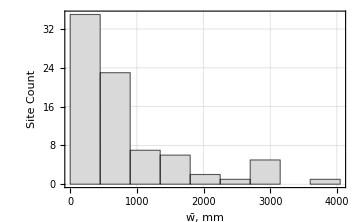

```mathematica
Print["Median "<>ToString[Median[wdata]]]
Print["Average "<>ToString[Mean[wdata]]]
Min[wdata]

wParam=Histogram[wdata ,{Range[0,Max[wdata],15*30]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"w̄, mm","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

```mathematica
BIdata =Join[Drop[LAmodelParametersImport[[All,3]],1],
Drop[FLmodelParametersImport[[All,3]],1]];
```

```mathematica
{0.212487,0.229068,0.317773,0.129074,0.242213,0.206954,0.208021,0.182785,0.209027,0.267989,0.12739,0.144178,0.0717554,0.282189,0.620055,0.237674,0.230313,0.228585,0.212141,0.328347,0.308706,0.382836,1.12451,0.140052,0.0790193,0.128401,0.119166,0.111717,0.528086,1.77596,0.0800382,0.204143,0.140005,0.167501,0.14028,0.38741,0.133962,0.190175,0.23628,0.0520293,0.406365,0.437612,0.771805,0.610534,0.283314,0.293847,0.196673,0.550042,1.13378,0.302937,10.0339,0.118602,0.0739714,1.19161,1.91035,0.882161,0.461563,0.376812,0.184369,0.149014,0.403538,0.234019679,0.129846,0.118191,0.167454,0.43909,0.286832,0.26799,0.108458,0.286791,0.18651,0.221894,0.527297,0.298915,0.979048,1.50601,0.670937,1.16865,0.689505,0.206817,0.20124}
```

{0.212487,0.229068,0.317773,0.129074,0.242213,0.206954,0.208021,0.182785,0.209027,0.267989,0.12739,0.144178,0.0717554,0.282189,0.620055,0.237674,0.230313,0.228585,0.212141,0.328347,0.308706,0.382836,1.12451,0.140052,0.0790193,0.128401,0.119166,0.111717,0.528086,1.77596,0.0800382,0.204143,0.140005,0.167501,0.14028,0.38741,0.133962,0.190175,0.23628,0.0520293,0.406365,0.437612,0.771805,0.610534,0.283314,0.293847,0.196673,0.550042,1.13378,0.302937,10.0339,0.118602,0.0739714,1.19161,1.91035,0.882161,0.461563,0.376812,0.184369,0.149014,0.403538,0.23402,0.129846,0.118191,0.167454,0.43909,0.286832,0.26799,0.108458,0.286791,0.18651,0.221894,0.527297,0.298915,0.979048,1.50601,0.670937,1.16865,0.689505,0.206817,0.20124}

Median 0.23628

Average 0.427579

0.0520293

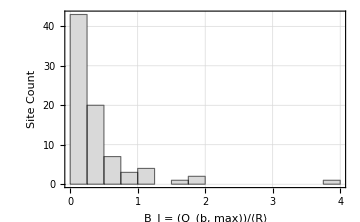

```mathematica
Print["Median "<>ToString[Median[BIdata ]]]
Print["Average "<>ToString[Mean[BIdata ]]]
Min[BIdata]

BIParam=Histogram[BIdata ,{Range[0,Max[BIdata ]+.2,.25]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"B_I = (Q_(b, max))/⟨R⟩","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

```mathematica
data3[[26]]
```

0.00408597

{0.00237793,0.0451519,0.364817,0.00614965,0.00183971,0.00422338,0.0028307,0.168028,0.00977978,0.170737,0.0116316,0.0176768,0.512931,0.175504,0.45882,0.14884,0.0251644,0.0065518,0.0426682,0.000337747,0.000896296,0.0384864,0.275519,0.0100883,0.00992168,0.0113756,0.00612802,0.00907265,0.0105748,0.00449194,0.00814495,0.00720992,0.0421429,0.0231521,0.00804512,0.0237942,0.00637786,0.0754356,0.0233425,0.00386074,0.0393426,0.00792864,0.000451338,0.0145621,0.00692432,0.00344804,0.00803586,0.0114806,0.0117599,0.00160143,0.000980741,0.000527831,0.0354584,0.00916133,0.0129431,0.012312,0.0252893,0.00383251,0.0324545,0.00576396,0.221309,0.0497926,0.0204943,0.0753684,0.00589703,0.00219645,0.0660402,0.0821895,0.00209553,0.0320993,0.00349163,0.00946234,0.286914,0.00376337,0.110915,0.00335328,0.00708853,0.00143284,0.0320862,0.0408481,0.163018}

Median 0.0113756

Average 0.0523239

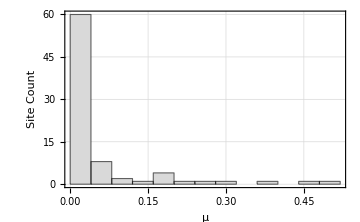

```mathematica
μdata =Join[Drop[LAmodelParametersImport[[All,5]],1],
Drop[FLmodelParametersImport[[All,5]],1]]
Print["Median "<>ToString[Median[μdata ]]]
Print["Average "<>ToString[Mean[μdata ]]]
μParam=Histogram[μdata ,{Range[0,Max[μdata ]+.01,.01*4]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"μ","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

{0.2,0.2,0.7,0.1,0.4,0.6,0.1,0.4,0.1,0.1,0.1,0.3,0.5,0.2,0.6,0.3,0.3,0.2,0.4,0.1,0.3,0.1,0.5,0.1,0.5,0.1,0.1,0.1,0.1,0.01,0.1,0.01,0.5,0.1,0.1,0.1,0.1,0.2,0.2,0.1,0.2,0.2,0.2,0.1,0.4,0.2,0.2,0.5,0.1,0.3,0.2,0.1,0.1,0.2,0.5,0.6,0.5,0.3,0.1,0.1,0.6,0.1,0.1,0.1,0.2,0.9,0.1,0.1,0.01,0.1,0.1,0.1,0.4,0.4,0.4,0.6,0.4,0.7,0.3,0.1,0.2}

Median 0.2

Average 0.252222

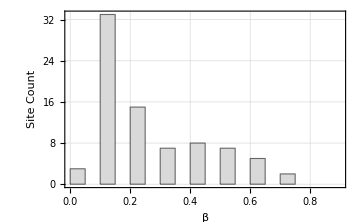

```mathematica
βdata =Join[Drop[LAmodelParametersImport[[All,6]],1],
Drop[FLmodelParametersImport[[All,6]],1]]
Print["Median "<>ToString[Median[βdata ]]]
Print["Average "<>ToString[Mean[βdata ]]]
βParam=Histogram[βdata ,{Range[0,Max[βdata ]*1.05,.05]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"β","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,12},ImageSize->Medium,PlotTheme->"Detailed"]
```

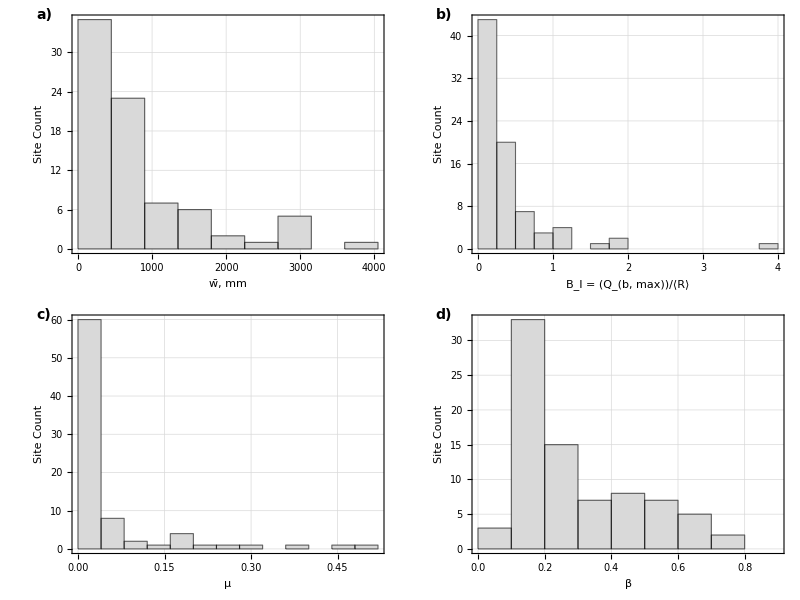

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]
(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[wParam,"a)"],labeledPlot[BIParam,"b)"]},{labeledPlot[μParam,"c)"],labeledPlot[βParam,"d)"]}},Spacings->2]
```

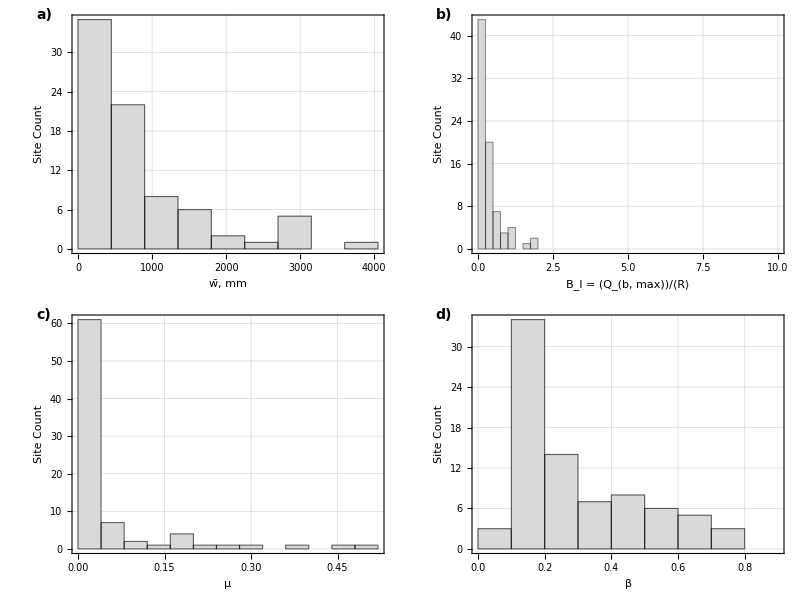

```mathematica
(*Function to add a label in the upper-left corner of a plot*)labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.09,1}]]}]]

(*Grid with labeled figures*)
grid=Grid[{{labeledPlot[wParam,"a)"],labeledPlot[BIParam,"b)"]},{labeledPlot[μParam,"c)"],labeledPlot[βParam,"d)"]}},Spacings->2]
```

```mathematica
Clear[pz,pzm,χPDF,χIavgN1,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,pχ,CC1N,ϑ]
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
(*χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)

χIavgN1[DI_?NumericQ,γ_?NumericQ]:=χIavgN1[DI,γ]=UnitStep[χIavg[DI,γ]-1]+UnitStep[1-χIavg[DI,γ]]χIavg[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
(*ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]*)
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI/(γs^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI/(γs^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI/γs^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI/γs)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI/γs)-LI/γs ξ10n,0],β==1}}]
(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γs,β,ϑ]=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Take the LOg and then exp to avoid a really small number in the denominator beyond the precision of the computer*)
CC1N[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1N[LI,γs,β,ϑ]=Exp[Evaluate[Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]]]]
pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γs,β,ϑ]=CC1[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
pχPlot[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))]+Log[(1-x)^((γs (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γs/LI))]+Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]],-700]]]
(**)
χavg[LI_,γs_,β_,ϑ_]:=γs/(γs+LI(1+γs(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+2+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
```

```mathematica
800/20
```

40

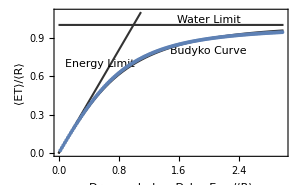

```mathematica
BudykoCurve1 = Table[{DI,DI χIavgN1[DI,γs μ]+ DI aPET[DI,γs μ] χavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]]}/.{γs->40, β->.25,BI->1,μ->.075},{DI,.025,3,.02}];
pt1=Plot[{Budyko[DI],1,DI},{DI,0,3},PlotRange->{0,1.1},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"⟨ET⟩/⟨R⟩",""},{"Dryness Index, D_I = E_max/⟨R⟩",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False];
(*New Value because of Climate shift*)
Label1=Graphics[{Text[Style["Budyko Curve",11,Background->None],{2,.8},{0,0},{1,.15}],Text[Style["Water Limit",11,Background->None],{2,1.04},{0,0},{1,0}],Text[Style["Energy Limit",11,Background->None],{.55,.7},{0,0},{1,2.75}]}];
FigAppendix2=Show[pt1,Label1,ListPlot[BudykoCurve1 ]]
```

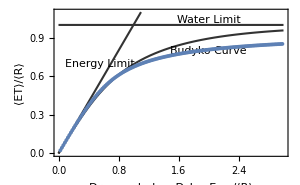

```mathematica
BudykoCurve1 = Table[{DI,DI χIavgN1[DI,γs μ]+ DI aPET[DI,γs μ] χavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]]}/.{γs->460/20, β->.1,BI->.25,μ->.012},{DI,.025,3,.02}];
pt1=Plot[{Budyko[DI],1,DI},{DI,0,3},PlotRange->{0,1.1},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"⟨ET⟩/⟨R⟩",""},{"Dryness Index, D_I = E_max/⟨R⟩",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False];
(*New Value because of Climate shift*)
Label1=Graphics[{Text[Style["Budyko Curve",11,Background->None],{2,.8},{0,0},{1,.15}],Text[Style["Water Limit",11,Background->None],{2,1.04},{0,0},{1,0}],Text[Style["Energy Limit",11,Background->None],{.55,.7},{0,0},{1,2.75}]}];
FigAppendix2=Show[pt1,Label1,ListPlot[BudykoCurve1 ]]
```